```mathematica
Table[stubbornForm5[k,"comp"]=GreaterEqual,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual}

```mathematica
Table[stubbornForm5[k,"comp"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual}

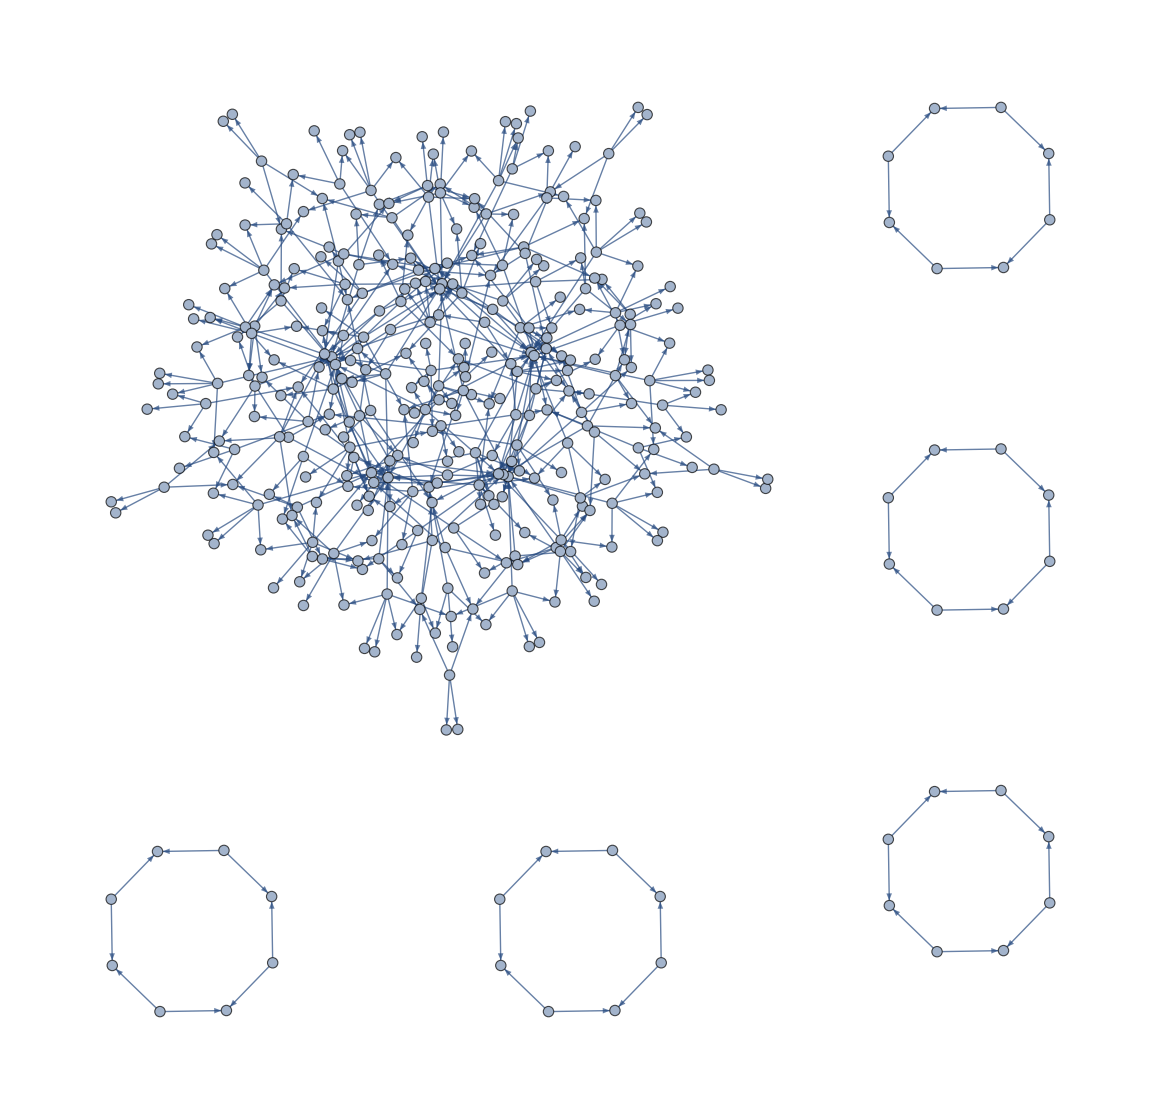

```mathematica
Graph[pr]
```

```mathematica
pr=Problems[stubbornForm5,0];
```

```mathematica
Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,pr]]],Length[ListofVars[stubbornForm5[#,"colofour"]]]==1&]
```

{36085,36166,29551,31738,31711,31714,36112,29533,38281,29560,38308,29527,29525,36086,29608,29633,36194,30253,36817,30334,36898,29605,29767,31954,29797,31984,49207,51475,49210,51478}

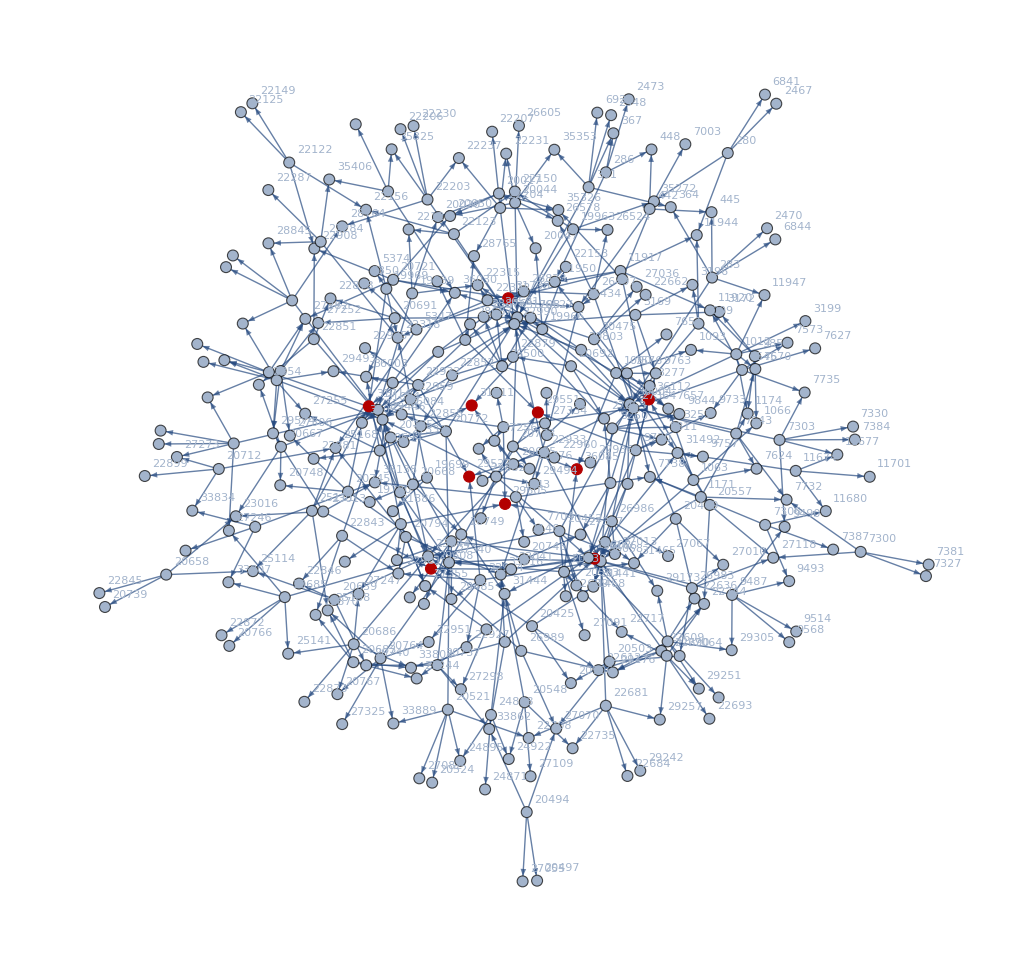

```mathematica
gg=VertexDelete[
Graph[pr,VertexLabels->"Name",GraphHighlight->Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,pr]]],Length[ListofVars[stubbornForm5[#,"colofour"]]]==1&]],
{38281,20785,38254,29533,38308,29506,20812,29560,23689,30253,36817,30172,36736,30334,36898,23770,31924,31954,31984,27580,27610,29767,29797,29737,49207,46939,49204,51475,49210,51472,46942,51478,29417,29525,29633,22964,23072,36086,36194,35978}]
```

```mathematica
VertexCount[gg]
```

345

```mathematica
Length[pr]
```

560

```mathematica
stubbornForm5[6841,"graph"]
```

-Graphics-

```mathematica
stubbornForm5[29439,"graph"]
```

-Graphics-

```mathematica
(ineqsthree52//AndToTable//ExpressionToTable)/.repcolofour5
```